```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
```

Importing from GitHub:  EpidemiologyModels.m

```mathematica
Clear[modelSEIQR];
modelSEIQR = 
  SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
ModelGridTableForm[modelSEIQR]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 100000
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==99999
2 | EP[0]==0
3 | IP[0]==1
4 | QP[0]==0
5 | RP[0]==0|>

## Getting Data

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
cievsRECData :=Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Recife/Monkeypox%20-%20Recife.csv", "Dataset", 
   "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];

dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
RECdataMap = cievsRECData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

#### Populações

```mathematica
(*pernambucoEntity = Entity["AdministrativeDivision", {"Pernambuco", "Brazil"}];
recifeEntity = Entity["City", {"Recife", "Pernambuco", "Brazil"}];
popProperty = "Population";*)

pernambucoPopulation = QuantityMagnitude[9674793]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
recifePopulation =  QuantityMagnitude[1661017]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
```

```mathematica
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

#### Confirmados

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

TimeSeries[…]

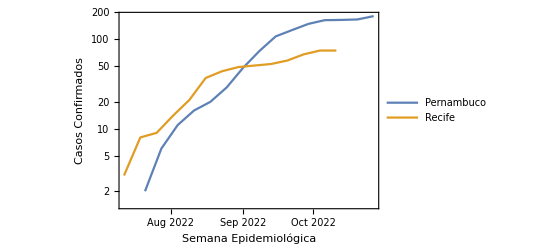

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 7, "Align"->Left];

SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 7, "Align"->Left]
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 7, "Align"->Left];
totalConfirmadosREC = 
 SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #Confirmados} &,  RECdataMap],TemporalRegularity -> True]], 7, "Align"->Left];
DateListLogPlot[Tooltip[{totalJoinedSmoothed ,totalConfirmadosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, GridLines -> Keys[confirmadosJoined],FrameLabel->{"Semana Epidemiológica","Casos Confirmados"}]
```

#### Prováveis

```mathematica
totalProvaveisPE =  SmoothPeriod[Accumulate[TimeSeries[ Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, PEdataMap], TemporalRegularity -> True]],7,"Align"->Left];
totalProvaveisREC = SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, RECdataMap], TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalProvaveisPE, totalProvaveisREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> Automatic, GridLines -> Automatic];
```

#### Suspeitos

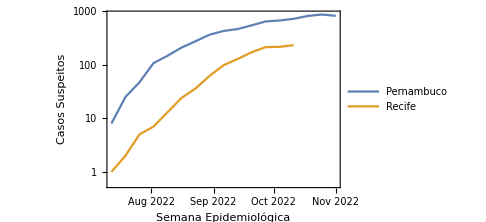

```mathematica
totalSuspeitosPE = 
  SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, 
      PEdataMap],TemporalRegularity -> True]],7,"Align"->Left];
totalSuspeitosREC = 
SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, RECdataMap], TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalSuspeitosPE, totalSuspeitosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, FrameLabel->{"Semana Epidemiológica","Casos Suspeitos"},ImageSize->Medium,GridLines -> False]
```

#### Notificados

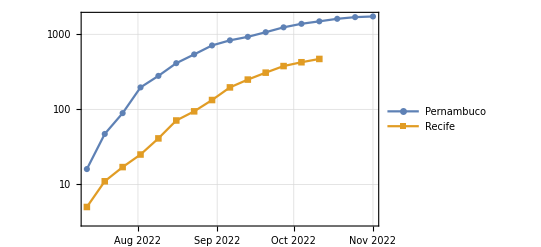

Keys::invrl: The argument joined is not a valid Association or a list of rules.

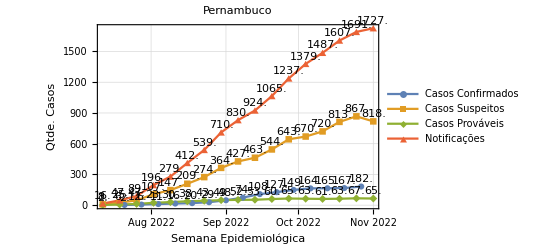

```mathematica
totalNotificadosPE = 
SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, 
      PEdataMap],TemporalRegularity -> True]],7,"Align"->Left];
totalNotificadosREC = 
SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, RECdataMap],TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalNotificadosPE, totalNotificadosREC} ],  Joined -> True, PlotLegends -> {"Pernambuco", "Recife"},  PlotMarkers -> Automatic, GridLines -> Automatic]

DateListPlot[{totalJoinedSmoothed ,totalSuspeitosPE, totalProvaveisPE, totalNotificadosPE}->{#2&},LabelingFunction->(Placed[Last@#1,Above]&), 
 Joined -> True, PlotLegends -> {"Casos Confirmados", "Casos Suspeitos", "Casos Prováveis", "Notificações" }, 
 PlotMarkers -> Automatic, GridLines -> Keys[joined],FrameLabel->{"Semana Epidemiológica","Qtde. Casos"}, PlotLabel->"Pernambuco"]
```

## Dados Literatura

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Modelos

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
initialExposed = Normal[totalProvaveisPE][[1]][[2]]
initialQuarantine = Normal[totalSuspeitosPE][[1]][[2]]
realEPData =  <|"Exposed"-> Ceiling[totalSuspeitosPE["Values"]] // Normal|>
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
realQPData = <|"Quarantine"-> Ceiling[totalProvaveisPE["Values"]] // Normal|>
allData = Join[realEPData,realIPData,realQPData]
lsFocusParams = {β, ζ, λ};
```

2

2

8

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867,818}|>

<|Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182}|>

<|Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67,65}|>

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867,818},Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182},Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67,65}|>

```mathematica
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquations = 
  Join[modelSEIQR["Equations"] //. 
    KeyDrop[modelSEIQR["RateRules"], lsFocusParams], 
   modelSEIQR["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations]
```

# | 1
1 | SP'[t]==0.2 QP[t]-4.24535×10^-6 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+4.24535×10^-6 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==235540.
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
aSol = Association@
  Flatten@ParametricNDSolve[lsActualEquations, 
    Head /@ Keys[modelSEIQR["Stocks"]], {t, 0,52}, lsFocusParams];
```

```mathematica
opts = {PlotRange -> All, PlotLegends -> None, PlotTheme -> "Detailed", 
   PerformanceGoal -> "Speed", ImageSize -> 400};
lsPopulationKeys = GetPopulationSymbols[modelSEIQR, __ ~~ "Population"];
Manipulate[
 DynamicModule[{lsPopulationPlots}, 
  lsPopulationPlots = 
   ParametricSolutionsPlots[modelSEIQR["Stocks"], 
    KeyTake[aSol, lsPopulationKeys], {contactRate, incubationPeriod, 
     infectionPeriod}, nWeeks,
    "LogPlot" -> popLogPlotQ, "Together" -> popTogetherQ, 
    "Derivatives" -> popDerivativesQ, "DerivativePrefix" -> "Δ",
     opts];
 
  Multicolumn[lsPopulationPlots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]],
   
 {{contactRate, 6.3, StringJoin["Contact rate of the infected population (β) ", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 1, 10, 1, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 8, "Infection Period (λ) in days"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week"}, 1, 52, 1, Appearance -> {"Open"}},
 {{popTogetherQ, True, "Plot populations together"}, {False, True}},
 {{popDerivativesQ, False, "Plot populations derivatives"}, {False, True}},
 {{popLogPlotQ, False, "LogPlot populations"}, {False, True}},
 {{nPlotColumns, 2, "Number of plot columns"}, Range[3]}, 
 ControlPlacement -> Left, ContinuousAction -> False]
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{modelSEIQR=modelSEIQR,equations,aSol,lsPopulationPlots},
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> population|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] ->  population -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
equations=Join[modelSEIQR["Equations"]//.KeyDrop[modelSEIQR["RateRules"],lsFocusParams],modelSEIQR["InitialConditions"]];
aSol=Association@Flatten@
ParametricNDSolve[equations,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];

lsPopulationPlots=
ParametricSolutionsPlots[
modelSEIQR["Stocks"],
KeyTake[aSol,GetPopulationSymbols[modelSEIQR, __ ~~ "Population"]],
{contactRate, incubationPeriod,infectionPeriod},nWeeks,"Together"->False,opts];
    
Show[lsPopulationPlots⟦3⟧,ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
],
{{population,estimatedInitialSusceptiblePopulation/100,"População"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"deslocamento de dados reais"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Taxa de Contágio (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Período de Incubação (ζ) em dias"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 7, "Período de Infecção (λ) em dias"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Semana Epidemiológica (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 2, "# de Colunas"}, Range[3]}, 
ControlPlacement->Left,ContinuousAction->False]
```

AssignRateRules::nargs: The first argument is expected to be a model association. The second argument is expected to be an association of rate rules.

AssignInitialConditions::nargs: The first argument is expected to be a model association. The second argument is expected to be an associations of initial condition rules.

KeyDrop::invrl: The argument $Failed[RateRules] is not a valid Association or a list of rules.

ReplaceRepeated::reps: {KeyDrop[$Failed[RateRules],{β,ζ,λ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceRepeated and $Failed at positions 1 and 2 are expected to be the same.

ParametricNDSolve::deqn: Equation or list of equations expected instead of Join[$Failed[Equations]//.KeyDrop[$Failed[RateRules],{β,ζ,λ}],$Failed[InitialConditions]] in the first argument Join[$Failed[Equations]//.KeyDrop[$Failed[RateRules],{β,ζ,λ}],$Failed[InitialConditions]].

KeyTake::invrl: The argument Association[Flatten[ParametricNDSolve[equations$209658,{SP,EP,IP,QP,RP},{t,0,100},lsFocusParams]]] is not a valid Association or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[{0.01,13,7},].

ParametricNDSolve::deqn: Equation or list of equations expected instead of equations in the first argument equations.

General::stop: Further output of ParametricNDSolve::deqn will be suppressed during this calculation.

KeyTake::invrl: The argument Association[Flatten[ParametricNDSolve[equations,{SP,EP,IP,QP,RP},{t,0,100},lsFocusParams]]] is not a valid Association or a list of rules.

AssignRateRules::nargs: The first argument is expected to be a model association. The second argument is expected to be an association of rate rules.

AssignInitialConditions::nargs: The first argument is expected to be a model association. The second argument is expected to be an associations of initial condition rules.

KeyDrop::invrl: The argument $Failed[RateRules] is not a valid Association or a list of rules.

ReplaceRepeated::reps: {KeyDrop[$Failed[RateRules],{β,ζ,λ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceRepeated and $Failed at positions 1 and 2 are expected to be the same.

ParametricNDSolve::deqn: Equation or list of equations expected instead of Join[$Failed[Equations]//.KeyDrop[$Failed[RateRules],{β,ζ,λ}],$Failed[InitialConditions]] in the first argument Join[$Failed[Equations]//.KeyDrop[$Failed[RateRules],{β,ζ,λ}],$Failed[InitialConditions]].

KeyTake::invrl: The argument Association[Flatten[ParametricNDSolve[equations$247328,{SP,EP,IP,QP,RP},{t,0,100},lsFocusParams]]] is not a valid Association or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[{0.01,13,7},].

ParametricNDSolve::deqn: Equation or list of equations expected instead of equations in the first argument equations.

General::stop: Further output of ParametricNDSolve::deqn will be suppressed during this calculation.

KeyTake::invrl: The argument Association[Flatten[ParametricNDSolve[equations,{SP,EP,IP,QP,RP},{t,0,100},lsFocusParams]]] is not a valid Association or a list of rules.

AssignRateRules::nargs: The first argument is expected to be a model association. The second argument is expected to be an association of rate rules.

AssignInitialConditions::nargs: The first argument is expected to be a model association. The second argument is expected to be an associations of initial condition rules.

KeyDrop::invrl: The argument $Failed[RateRules] is not a valid Association or a list of rules.

ReplaceRepeated::reps: {KeyDrop[$Failed[RateRules],{β,α1,α2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceRepeated and $Failed at positions 1 and 2 are expected to be the same.

ParametricNDSolve::deqn: Equation or list of equations expected instead of Join[$Failed[Equations]//.KeyDrop[$Failed[RateRules],{β,α1,α2}],$Failed[InitialConditions]] in the first argument Join[$Failed[Equations]//.KeyDrop[$Failed[RateRules],{β,α1,α2}],$Failed[InitialConditions]].

KeyTake::invrl: The argument Association[Flatten[ParametricNDSolve[equations$97513298,{SP,EP,IP,QP,RP},{t,0,100},lsFocusParams]]] is not a valid Association or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[{0.01,13,7},].

ParametricNDSolve::deqn: Equation or list of equations expected instead of equations in the first argument equations.

General::stop: Further output of ParametricNDSolve::deqn will be suppressed during this calculation.

KeyTake::invrl: The argument Association[Flatten[ParametricNDSolve[equations,{SP,EP,IP,QP,RP},{t,0,100},lsFocusParams]]] is not a valid Association or a list of rules.

### Otimização de β

```mathematica
expostosJoined = Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, PEdataMap];
```

```mathematica
totalInfectedOptimized = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7,"Align"->Left]
```

TimeSeries[…]

```mathematica
firstDateInfected = First @ First@Normal[totalInfectedOptimized];
lastDateInfected = First @  Last@Normal[totalInfectedOptimized];
DateObject[First @ First@Normal[totalInfectedOptimized]]
```

Thu 21 Jul 2022 00:00:00GMT-3

```mathematica
ClearAll[modelSEIQR2];
modelSEIQR2 = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation/100|>];
modelSEIQR2 = SetInitialConditions[modelSEIQR2,
   <|SP[0] ->  estimatedInitialSusceptiblePopulation/100-initialExposed- initialInfected-initialQuarantine ,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
lsActualEquations2 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],lsFocusParams],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations2]
asol2 = ParametricNDSolve[lsActualEquations2,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000424535 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+0.000424535 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==2343.52
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

#### Dados Totais, ajuste estatístico de β, ζ e λ

```mathematica
fitInfectedData={ToModelTime[firstDateInfected, #1], #2}& @@@ Normal[totalInfectedOptimized] //Echo[#, "", Multicolumn]&;
(*fitExposedData={toModelTime[firstDateExposed, #1], #2}& @@@ Normal[totalExpostosOptimized] //Echo[#, "", Multicolumn]&;*)
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
infectedSol= IP[β,ζ,λ] /.asol2;
exposedSol = EP[β,ζ,λ] /.asol2;
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.432795 | 0.144859 | 2.98769 | 0.0113227
ζ | 5. | 6.2881 | 0.795153 | 0.441969
λ | 9.09259 | 1.48665 | 6.11614 | 0.0000520681

0.987511

0.984389

{β→0.432795,ζ→5.,λ→9.09259}

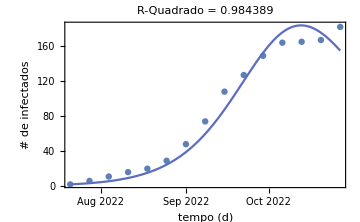

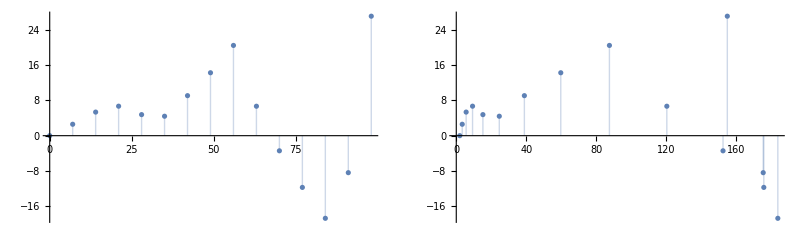

```mathematica
fitInfected=NonlinearModelFit[fitInfectedData,{infectedSol[t],5<=ζ<=21 && 0<=λ<=21 } ,{{β, 1.22}, {ζ,10},{λ,14}},t, Method->Automatic];
fitInfected["ParameterTable"]
fitInfected["RSquared"]
fitInfected["AdjustedRSquared"]
fitInfected["BestFitParameters"]
FitWithDataPlot[fitInfected,{firstDateInfected,lastDateInfected} ]
ResidualsPlot[fitInfected]
(*ModelSensitivityPlot[ infectedSol,fitInfected,{{0,100},{-15,190}},{0.1,1,1}]*)
```

#### Ajuste estatístico, só β

```mathematica
lsActualEquations3 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],{β}],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations3]
asol3 = ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,0,120},{β}];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000424535 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/13+0.000424535 β IP[t] SP[t]
3 | IP'[t]==EP[t]/13-(4 IP[t])/31
4 | QP'[t]==EP[t]/13-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2343.52
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
totalInfectedOptimized2 = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],21, "Align"-> Left] // Normal
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfected2 = First @ First@Normal[totalInfectedOptimized2]
lastDateInfected2 = First @  Last@ Normal[totalInfectedOptimized2]
fitInfectedData2={ToModelTime[firstDateInfected2, #1], #2}& @@@ Normal[totalInfectedOptimized2] //Echo[#, "", Multicolumn]&;
```

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

Thu 21 Jul 2022 00:00:00GMT-3

Thu 13 Oct 2022 00:00:00GMT-3

{0,8} | {42,77} | {84,171}
{21,23} | {63,147} |

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

NonlinearModelFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.680064 | 0.0220259 | 30.8756 | 6.5563×10^-6

0.974293

0.967866

{β→0.680064}

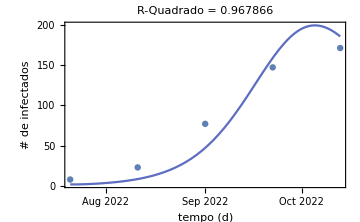

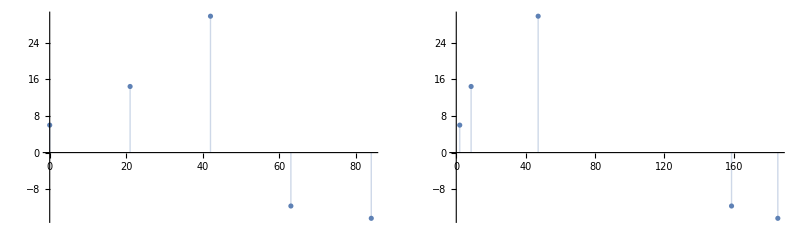

ModelSensitivityPlot[ParametricFunction[<>][β],FittedModel[InterpolatingFunction[…][t]],{{0,84},{-15,180}},{0.1}]

```mathematica
solution := ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,First@First@fitInfectedData2,First@Last@fitInfectedData2},{β}];
{susceptible,infectedSol2}= {SP[β],IP[β]} /.solution;
current = Take[totalInfectedOptimized2,5]
fitInfected2=NonlinearModelFit[{ToModelTime[First@First@Normal[current], #1], #2}& @@@ Normal[current],infectedSol2[t],{{β,1}},t, Method->"QuasiNewton"];
fitInfected2["ParameterTable"]
fitInfected2["RSquared"]
fitInfected2["AdjustedRSquared"]
fitInfected2["BestFitParameters"]
FitWithDataPlot[fitInfected2,{First@First@Normal[current],First@Last@Normal[current]} ]
ResidualsPlot[fitInfected2]
ModelSensitivityPlot[ infectedSol2,fitInfected2,{{First@First@fitInfectedData2,First@Last@fitInfectedData2},{-15,180}},{0.1}]

(*susceptible=SP[N[First@Values[fitInfected2["BestFitParameters"]]]][84] /.solution*)
```

#### Com β Dinâmico

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];
AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
AppendTo[model["InitialConditions"], NIP[t /; t<=0]==1];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], ρ'[t]==((NIP[t-3] +NIP[t-2]+ NIP[t-1])/(NIP[t-3-ζ] + NIP[t-2-ζ]+NIP[t-1-ζ]))];
AppendTo[model["Equations"], β'[t]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/7)/10 ];
AppendTo[model["InitialConditions"], ρ[t /; t<=0]==0];
AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> 7|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100]-initialExposed- initialInfected-initialQuarantine ,
EP[0] -> initialExposed,
QP[0] -> initialQuarantine
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], {α1,α2}],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

{SP'[t]==0.2 QP[t]-(IP[t] SP[t] β[t])/2356,EP'[t]==-((α1+α2) EP[t])+(IP[t] SP[t] β[t])/2356,IP'[t]==α1 EP[t]-IP[t]/7,QP'[t]==α2 EP[t]-0.342857 QP[t],RP'[t]==IP[t]/7+QP[t]/7,NIP'[t]==-IP[-1+t]+IP[t],ρ'[t]==(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t]),β'[t]==1/70 (ρ[-6+t]+ρ[-5+t]+ρ[-4+t]+ρ[-3+t]+ρ[-2+t]+ρ[t]),SP[0]==2344,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0,NIP[t/;t≤0]==1,ρ[t/;t≤0]==0,β[t/;t≤0]==0.001}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population
7 | NIP[t] | Newly Infected Population,Rates→# | Symbol | Description
1 | β[t] | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(IP[t] SP[t] β[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(IP[t] SP[t] β[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t]
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | ρ'[t]==(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-3+t-ζ]+NIP[-2+t-ζ]+NIP[-1+t-ζ])
8 | β'[t]==1/70 (ρ[-6+t]+ρ[-5+t]+ρ[-4+t]+ρ[-3+t]+ρ[-2+t]+ρ[t]),RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | α1 | 1/ζ
3 | α2 | 1/ζ
4 | φ | 0.2
5 | τ | γ
6 | γ | 1/λ
7 | ζ | 13
8 | λ | 7,InitialConditions→# | Equation
1 | SP[0]==2344
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0
6 | NIP[t/;t≤0]==1
7 | ρ[t/;t≤0]==0
8 | β[t/;t≤0]==0.001|>

```mathematica
asolDynamicBeta = Association@Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP,ρ, β},{t,0,100},{α1, α2}, Method->"StiffnessSwitching", MaxSteps->Infinity]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>],NIP→ParametricFunction[<>],ρ→ParametricFunction[<>],β→ParametricFunction[<>]|>

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(IP[t] SP[t] β[t])/2356
2 | EP'[t]==-((α1+α2) EP[t])+(IP[t] SP[t] β[t])/2356
3 | IP'[t]==α1 EP[t]-IP[t]/7
4 | QP'[t]==α2 EP[t]-0.342857 QP[t]
5 | RP'[t]==IP[t]/7+QP[t]/7
6 | NIP'[t]==Max[IP[-1+t],IP[t]]-Min[IP[-1+t],IP[t]]
7 | ρ'[t]==(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])
8 | β'[t]==1/70 (ρ[-6+t]+ρ[-5+t]+ρ[-4+t]+ρ[-3+t]+ρ[-2+t]+ρ[t])
9 | SP[0]==2344
10 | EP[0]==2
11 | IP[t/;t≤0]==2
12 | QP[0]==8
13 | RP[0]==0
14 | NIP[t/;t≤0]==1
15 | ρ[t/;t≤0]==0
16 | β[t/;t≤0]==0.001

```mathematica
allValues =Map[ParametricFunctionValues[#,<| α1->0.04, α2-> 0.04|>, {0,100,1}]&, asolDynamicBeta]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

<|SP→{{0,2344.},{1,2345.36},{2,2346.3},{3,2346.94},{4,2347.3},{5,2347.39},{6,2347.22},{7,2346.73},{8,2345.85},{9,2344.46},{10,2342.37},{11,2339.23},{12,2334.4},{13,2326.75},{14,2314.15},{15,2292.6},{16,2254.34},{17,2184.24},{18,2053.53},{19,1812.88},{20,1403.3},{21,836.21},{22,315.975},{23,67.0062},{24,14.4766},{25,8.33056},{26,6.25811},{27,4.67383},{28,3.4479},{29,2.53112},{30,1.86495},{31,1.38982},{32,1.05365},{33,0.81556},{34,0.645565},{35,0.522584},{36,0.432144},{37,0.364407},{38,0.312694},{39,0.272449},{40,0.240542},{41,0.214796},{42,0.193686},{43,0.176123},{44,0.161322},{45,0.148704},{46,0.137837},{47,0.128394},{48,0.120122},{49,0.112821},{50,0.106337},{51,0.100542},{52,0.0953353},{53,0.0906341},{54,0.0863697},{55,0.0824774},{56,0.0789327},{57,0.0756725},{58,0.0726702},{59,0.0698969},{60,0.0673277},{61,0.0649411},{62,0.0627183},{63,0.0606432},{64,0.0587017},{65,0.0568812},{66,0.0551707},{67,0.0535607},{68,0.0520424},{69,0.0506082},{70,0.0492513},{71,0.0479655},{72,0.0467454},{73,0.0455858},{74,0.0444828},{75,0.0434318},{76,0.0424293},{77,0.0414721},{78,0.040557},{79,0.0396813},{80,0.0388425},{81,0.0380382},{82,0.0372664},{83,0.0365251},{84,0.0358125},{85,0.0351269},{86,0.0344667},{87,0.0338307},{88,0.0332135},{89,0.0326257},{90,0.0320543},{91,0.0315024},{92,0.0309688},{93,0.0304527},{94,0.0299531},{95,0.0294694},{96,0.0290007},{97,0.0285464},{98,0.0281058},{99,0.0276783},{100,0.0272633}},EP→{{0,2.},{1,1.85235},{2,1.73889},{3,1.67771},{4,1.69661},{5,1.83254},{6,2.13012},{7,2.64505},{8,3.45243},{9,4.65957},{10,6.44269},{11,9.11112},{12,13.2203},{13,19.7833},{14,30.6856},{15,49.5165},{16,83.2454},{17,145.493},{18,262.163},{19,477.199},{20,840.742},{21,1331.18},{22,1742.98},{23,1868.62},{24,1802.62},{25,1701.31},{26,1605.86},{27,1518.04},{28,1436.59},{29,1360.54},{30,1289.21},{31,1222.09},{32,1158.78},{33,1098.97},{34,1042.4},{35,988.855},{36,938.134},{37,890.066},{38,844.499},{39,801.289},{40,760.308},{41,721.435},{42,684.557},{43,649.571},{44,616.376},{45,584.879},{46,554.994},{47,526.637},{48,499.73},{49,474.197},{50,449.97},{51,426.98},{52,405.165},{53,384.464},{54,364.821},{55,346.182},{56,328.495},{57,311.711},{58,295.785},{59,280.673},{60,266.333},{61,252.725},{62,239.813},{63,227.56},{64,215.933},{65,204.901},{66,194.432},{67,184.498},{68,175.071},{69,166.126},{70,157.638},{71,149.584},{72,141.941},{73,134.689},{74,127.807},{75,121.277},{76,115.081},{77,109.201},{78,103.622},{79,98.3273},{80,93.3035},{81,88.5364},{82,84.0128},{83,79.7204},{84,75.6473},{85,71.7823},{86,68.1148},{87,64.6347},{88,61.3324},{89,58.1988},{90,55.2253},{91,52.4038},{92,49.7264},{93,47.1858},{94,44.7751},{95,42.4875},{96,40.3168},{97,38.257},{98,36.3024},{99,34.4477},{100,32.6878}},IP→{{0,2.},{1,1.80541},{2,1.63182},{3,1.47803},{4,1.34387},{5,1.23037},{6,1.13999},{7,1.07667},{8,1.04629},{9,1.05727},{10,1.12205},{11,1.26031},{12,1.50485},{13,1.91262},{14,2.58568},{15,3.71168},{16,5.64442},{17,9.06368},{18,15.2798},{19,26.7298},{20,47.3878},{21,81.5888},{22,128.904},{23,180.009},{24,224.718},{25,260.06},{26,287.009},{27,306.961},{28,321.109},{29,330.444},{30,335.793},{31,337.852},{32,337.21},{33,334.36},{34,329.724},{35,323.654},{36,316.451},{37,308.368},{38,299.617},{39,290.377},{40,280.8},{41,271.011},{42,261.115},{43,251.198},{44,241.331},{45,231.574},{46,221.972},{47,212.564},{48,203.379},{49,194.44},{50,185.765},{51,177.366},{52,169.25},{53,161.423},{54,153.886},{55,146.641},{56,139.683},{57,133.009},{58,126.615},{59,120.494},{60,114.64},{61,109.044},{62,103.7},{63,98.5979},{64,93.7307},{65,89.0895},{66,84.6658},{67,80.451},{68,76.4368},{69,72.6149},{70,68.9771},{71,65.5156},{72,62.2225},{73,59.0905},{74,56.1123},{75,53.2807},{76,50.5892},{77,48.031},{78,45.6001},{79,43.2902},{80,41.0957},{81,39.0111},{82,37.0309},{83,35.1502},{84,33.364},{85,31.6679},{86,30.0572},{87,28.5279},{88,27.0759},{89,25.6973},{90,24.3885},{91,23.146},{92,21.9666},{93,20.847},{94,19.7842},{95,18.7754},{96,17.8179},{97,16.9091},{98,16.0465},{99,15.2278},{100,14.4508}},QP→{{0,8.},{1,5.74293},{2,4.13656},{3,2.99349},{4,2.18148},{5,1.60778},{6,1.20796},{7,0.937977},{8,0.768788},{9,0.682828},{10,0.672362},{11,0.740017},{12,0.902113},{13,1.19642},{14,1.69807},{15,2.55146},{16,4.03461},{17,6.68755},{18,11.5555},{19,20.5727},{20,36.8073},{21,63.2048},{22,97.9451},{23,131.603},{24,155.753},{25,169.774},{26,176.376},{27,177.97},{28,176.245},{29,172.361},{30,167.115},{31,161.053},{32,154.547},{33,147.849},{34,141.128},{35,134.497},{36,128.029},{37,121.768},{38,115.742},{39,109.965},{40,104.442},{41,99.1717},{42,94.151},{43,89.373},{44,84.8294},{45,80.5112},{46,76.4089},{47,72.5129},{48,68.8136},{49,65.3017},{50,61.9681},{51,58.804},{52,55.801},{53,52.951},{54,50.2464},{55,47.6797},{56,45.244},{57,42.9327},{58,40.7393},{59,38.658},{60,36.683},{61,34.8088},{62,33.0304},{63,31.3428},{64,29.7415},{65,28.2219},{66,26.78},{67,25.4117},{68,24.1134},{69,22.8814},{70,21.7123},{71,20.603},{72,19.5503},{73,18.5514},{74,17.6036},{75,16.7041},{76,15.8507},{77,15.0408},{78,14.2723},{79,13.5431},{80,12.8512},{81,12.1946},{82,11.5715},{83,10.9803},{84,10.4193},{85,9.88692},{86,9.38177},{87,8.90244},{88,8.44759},{89,8.01599},{90,7.60643},{91,7.21781},{92,6.84903},{93,6.49911},{94,6.16706},{95,5.85197},{96,5.55299},{97,5.26928},{98,5.00007},{99,4.74462},{100,4.50221}},RP→{{0,0.},{1,1.24407},{2,2.18853},{3,2.91509},{4,3.48275},{5,3.93462},{6,4.30299},{7,4.61291},{8,4.88495},{9,5.13741},{10,5.38825},{11,5.65728},{12,5.96926},{13,6.35893},{14,6.87984},{15,7.62073},{16,8.73682},{17,10.5109},{18,13.4727},{19,18.6203},{20,27.7677},{21,43.8194},{22,70.1922},{23,108.762},{24,158.436},{25,216.529},{26,280.494},{27,348.355},{28,418.613},{29,490.125},{30,562.017},{31,633.618},{32,704.412},{33,774.006},{34,842.1},{35,908.471},{36,972.954},{37,1035.43},{38,1095.83},{39,1154.1},{40,1210.21},{41,1264.17},{42,1315.98},{43,1365.68},{44,1413.3},{45,1458.89},{46,1502.49},{47,1544.16},{48,1583.96},{49,1621.95},{50,1658.19},{51,1692.75},{52,1725.69},{53,1757.07},{54,1786.96},{55,1815.42},{56,1842.5},{57,1868.27},{58,1892.79},{59,1916.1},{60,1938.28},{61,1959.36},{62,1979.39},{63,1998.44},{64,2016.54},{65,2033.73},{66,2050.07},{67,2065.59},{68,2080.33},{69,2094.33},{70,2107.62},{71,2120.25},{72,2132.24},{73,2143.62},{74,2154.43},{75,2164.69},{76,2174.44},{77,2183.69},{78,2192.47},{79,2200.8},{80,2208.71},{81,2216.22},{82,2223.35},{83,2230.11},{84,2236.53},{85,2242.63},{86,2248.41},{87,2253.9},{88,2259.11},{89,2264.06},{90,2268.75},{91,2273.2},{92,2277.43},{93,2281.44},{94,2285.24},{95,2288.86},{96,2292.28},{97,2295.54},{98,2298.62},{99,2301.55},{100,2304.33}},NIP→{{0,1.},{1,1.09912},{2,1.28307},{3,1.4467},{4,1.59071},{5,1.71468},{6,1.81689},{7,1.89414},{8,1.94157},{9,1.95474},{10,1.99135},{11,2.0908},{12,2.27868},{13,2.59864},{14,3.12783},{15,4.00646},{16,5.49607},{17,8.09525},{18,12.7657},{19,21.3336},{20,36.9986},{21,64.1551},{22,105.331},{23,155.563},{24,204.033},{25,244.055},{26,275.08},{27,298.422},{28,315.382},{29,327.048},{30,334.326},{31,337.977},{32,338.807},{33,340.591},{34,344.366},{35,349.746},{36,356.406},{37,364.068},{38,372.502},{39,381.511},{40,390.93},{41,400.623},{42,410.473},{43,420.386},{44,430.284},{45,440.1},{46,449.784},{47,459.291},{48,468.59},{49,477.653},{50,486.461},{51,494.999},{52,503.258},{53,511.229},{54,518.911},{55,526.302},{56,533.404},{57,540.219},{58,546.752},{59,553.009},{60,558.997},{61,564.721},{62,570.19},{63,575.413},{64,580.396},{65,585.15},{66,589.682},{67,594.},{68,598.114},{69,602.031},{70,605.761},{71,609.31},{72,612.686},{73,615.898},{74,618.953},{75,621.857},{76,624.618},{77,627.242},{78,629.736},{79,632.106},{80,634.358},{81,636.497},{82,638.529},{83,640.459},{84,642.292},{85,644.033},{86,645.686},{87,647.256},{88,648.746},{89,650.161},{90,651.504},{91,652.78},{92,653.99},{93,655.14},{94,656.231},{95,657.266},{96,658.249},{97,659.182},{98,660.068},{99,660.908},{100,661.706}},ρ→{{0,0.},{1,1.},{2,2.01112},{3,3.08651},{4,4.28409},{5,5.64399},{6,7.15775},{7,8.80524},{8,10.5652},{9,12.4139},{10,14.3235},{11,16.2701},{12,18.2547},{13,20.3145},{14,22.5265},{15,24.9793},{16,27.7036},{17,30.7764},{18,34.4176},{19,39.1527},{20,45.9115},{21,56.3459},{22,73.3484},{23,101.507},{24,146.553},{25,212.7},{26,299.248},{27,399.459},{28,503.269},{29,600.649},{30,683.903},{31,748.918},{32,795.394},{33,825.98},{34,844.77},{35,855.839},{36,862.354},{37,866.38},{38,869.097},{39,871.128},{40,872.793},{41,874.259},{42,875.615},{43,876.911},{44,878.179},{45,879.439},{46,880.707},{47,881.994},{48,883.302},{49,884.628},{50,885.963},{51,887.301},{52,888.639},{53,889.97},{54,891.294},{55,892.607},{56,893.908},{57,895.196},{58,896.471},{59,897.733},{60,898.982},{61,900.218},{62,901.441},{63,902.652},{64,903.852},{65,905.04},{66,906.218},{67,907.385},{68,908.543},{69,909.693},{70,910.833},{71,911.966},{72,913.091},{73,914.209},{74,915.32},{75,916.425},{76,917.524},{77,918.617},{78,919.705},{79,920.788},{80,921.867},{81,922.941},{82,924.011},{83,925.077},{84,926.14},{85,927.199},{86,928.254},{87,929.307},{88,930.357},{89,931.404},{90,932.448},{91,933.49},{92,934.53},{93,935.568},{94,936.604},{95,937.637},{96,938.669},{97,939.699},{98,940.728},{99,941.755},{100,942.781}},β→{{0,0.001},{1,0.00814286},{2,0.0296113},{3,0.0730534},{4,0.154134},{5,0.289765},{6,0.498415},{7,0.800389},{8,1.21086},{9,1.73954},{10,2.39704},{11,3.19367},{12,4.13858},{13,5.23952},{14,6.50354},{15,7.93793},{16,9.55098},{17,11.3534},{18,13.3608},{19,15.5979},{20,18.105},{21,20.9504},{22,24.2527},{23,28.2198},{24,33.2021},{25,39.7435},{26,48.605},{27,60.7469},{28,77.2694},{29,99.3039},{30,127.853},{31,163.614},{32,206.825},{33,257.204},{34,314.002},{35,376.156},{36,442.481},{37,511.837},{38,583.261},{39,656.016},{40,729.597},{41,803.686},{42,878.097},{43,952.729},{44,1027.53},{45,1102.47},{46,1177.53},{47,1252.71},{48,1328.},{49,1403.4},{50,1478.91},{51,1554.53},{52,1630.26},{53,1706.11},{54,1782.07},{55,1858.14},{56,1934.33},{57,2010.63},{58,2087.04},{59,2163.57},{60,2240.2},{61,2316.95},{62,2393.81},{63,2470.77},{64,2547.84},{65,2625.02},{66,2702.3},{67,2779.69},{68,2857.17},{69,2934.76},{70,3012.46},{71,3090.25},{72,3168.14},{73,3246.13},{74,3324.21},{75,3402.39},{76,3480.67},{77,3559.05},{78,3637.52},{79,3716.09},{80,3794.75},{81,3873.5},{82,3952.35},{83,4031.29},{84,4110.32},{85,4189.44},{86,4268.66},{87,4347.96},{88,4427.36},{89,4506.85},{90,4586.43},{91,4666.1},{92,4745.86},{93,4825.71},{94,4905.65},{95,4985.67},{96,5065.79},{97,5146.},{98,5226.29},{99,5306.67},{100,5387.15}}|>

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{alpha1,alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[allData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.03, "Alpha 1(α1)"}, 0, 1, 0.01, 
  Appearance -> {"Open"}},
 {{alpha2, 0.03, "Alpha 2(α2)"}, 0, 1, 0.01, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, True, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

Part::partw: Part 3 of … does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Part::partw: Part 3 of … does not exist.

PadRealData::nargs: The first argument is expected to be an association, second and third Integers representing Incubation Period and Infectious Period

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Right] // Normal
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
```

{{Thu 28 Jul 2022 00:00:00GMT-3,2},{Thu 4 Aug 2022 00:00:00GMT-3,6},{Thu 11 Aug 2022 00:00:00GMT-3,11},{Thu 18 Aug 2022 00:00:00GMT-3,16},{Thu 25 Aug 2022 00:00:00GMT-3,20},{Thu 1 Sep 2022 00:00:00GMT-3,29},{Thu 8 Sep 2022 00:00:00GMT-3,48},{Thu 15 Sep 2022 00:00:00GMT-3,74},{Thu 22 Sep 2022 00:00:00GMT-3,108},{Thu 29 Sep 2022 00:00:00GMT-3,127},{Thu 6 Oct 2022 00:00:00GMT-3,149},{Thu 13 Oct 2022 00:00:00GMT-3,164},{Thu 20 Oct 2022 00:00:00GMT-3,165},{Thu 27 Oct 2022 00:00:00GMT-3,167},{Thu 3 Nov 2022 00:00:00GMT-3,182}}

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP,ρ,β},{t,0,21},{α1,α2}, Method->{"ParametricCaching" -> None}]];
{infectedSolDynamic, betaSolDynamic, propagationRate}= {IP[α1,α2], β[α1,α2],ρ[α1,α2]} /.newlyInfectedSol;
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,4]
```

{{Thu 28 Jul 2022 00:00:00GMT-3,2},{Thu 4 Aug 2022 00:00:00GMT-3,6},{Thu 11 Aug 2022 00:00:00GMT-3,11},{Thu 18 Aug 2022 00:00:00GMT-3,16}}

```mathematica
fitInfectedDynamic=NonlinearModelFit[{ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic],{infectedSolDynamic[t], α2 >0},{{α1,0.04},{α2,0.02}},t, Method->Automatic]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel[InterpolatingFunction[…][t]]

{α1→0.0211258,α2→1.12099×10^-6}

0.746503

0.493006

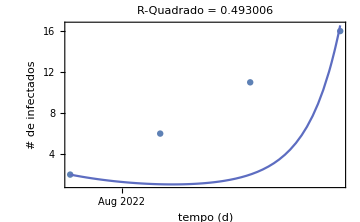

```mathematica
Quiet @ fitInfectedDynamic["BestFitParameters"]
Quiet @fitInfectedDynamic["RSquared"]
Quiet @fitInfectedDynamic["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

```mathematica
{β-> betaSolDynamic[0] /. Quiet @ fitInfectedDynamic["BestFitParameters"]}
{ρ-> propagationRate[0] /. Quiet @ fitInfectedDynamic["BestFitParameters"]}
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{β→0.001}

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{ρ→1.}

## Modelo Final

```mathematica
finalFit = fitInfected2;
finalBeta = Values @@ finalFit["BestFitParameters"] *10
```

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation,  β->finalBeta|>];
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]];
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}]
```

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}, {β}] ;
allValues =Map[ParametricFunctionValues[#,<|β-> finalBeta|>, 60]&, aSolForPeaks]
peaks = Map[FindPeaks[Last/@#]&,allValues]
(*lsFinal = ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],KeyTake[aSolFinal,GetPopulationSymbols[modelSEIQRFinal, __ ~~ "Population"]],{β},100,"Together"->True,optsFinal]*)
(*ListLinePlot[{allValues[[1]], peaks[[1]]}&,
Joined->{True, False},
PlotStyle->{Automatic, PointSize[.03]}]*)
```

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
(*Map[ParametricSolutionsPlots[#,<|β-> finalBeta|>, 100]&, aSolFinal]*)
(*PadRealData[peaks,13,7.75]*)
(*Show[lsFinal, peaks,PlotStyle->{Blue,Black,Red}]*)
(*Show[Plot[allValues,Joined->False,PlotRange->All]]*)
optsFinal={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{incubationPeriod=13,infectionPeriod=8,nWeeks=60,padOffset=-8},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,None,nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]], ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```